## Node sequence ΣnTETXISO

## Brown ΣnTETXISO (U for nm4 is closest XISO)

T is Brown

Path nodes are {TRIV,MONO,ORTH,TET,XISO,ISO}

dt = 0.2

UforNM4 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

#### separate plots for nm2, nm3, nm4 for all Σ

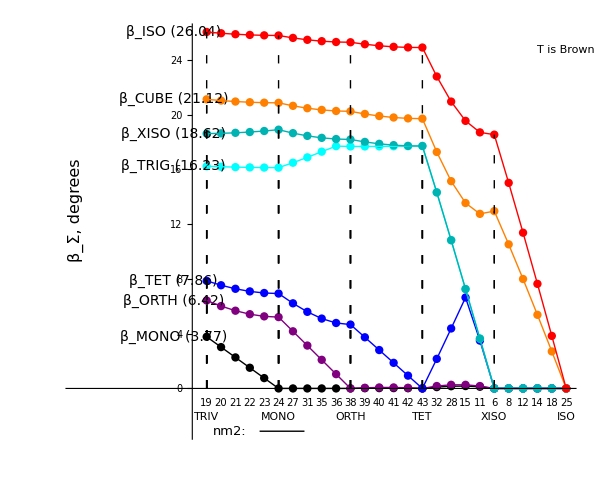

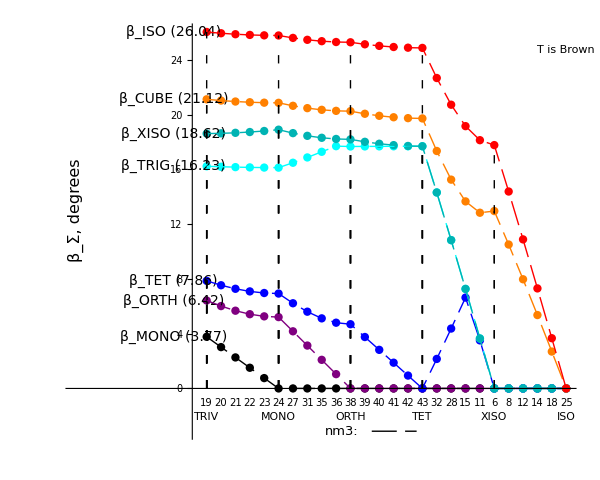

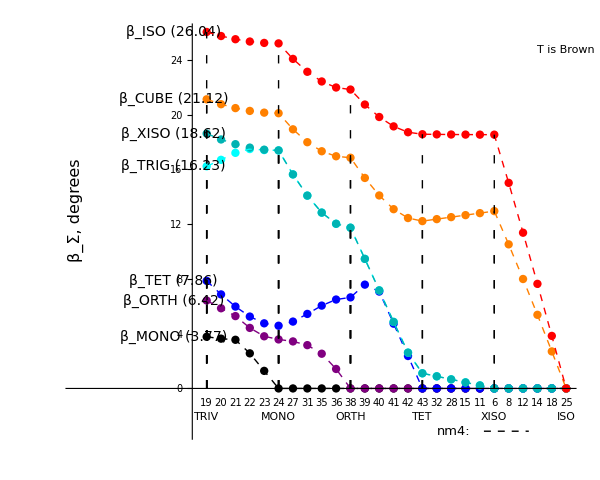

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

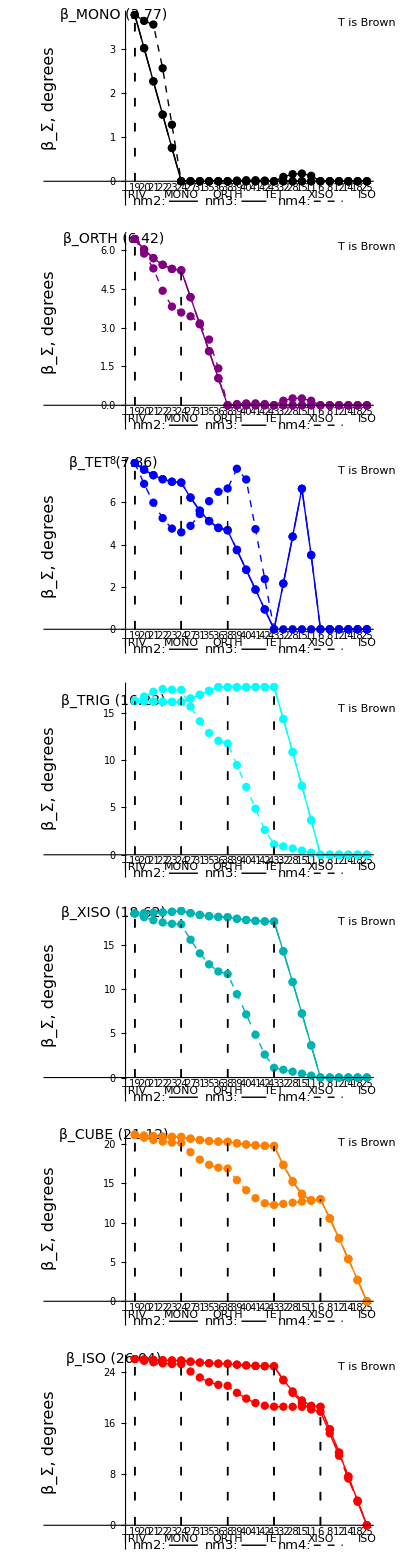

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

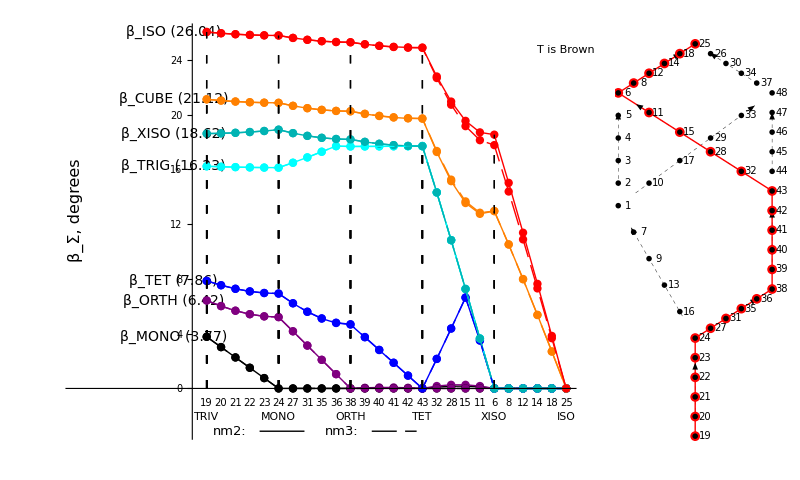

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,Σn]},ImageSize->800,Spacings->0]
```

#### Four node sequences for nm2 and nm4 (based on AllPoints)

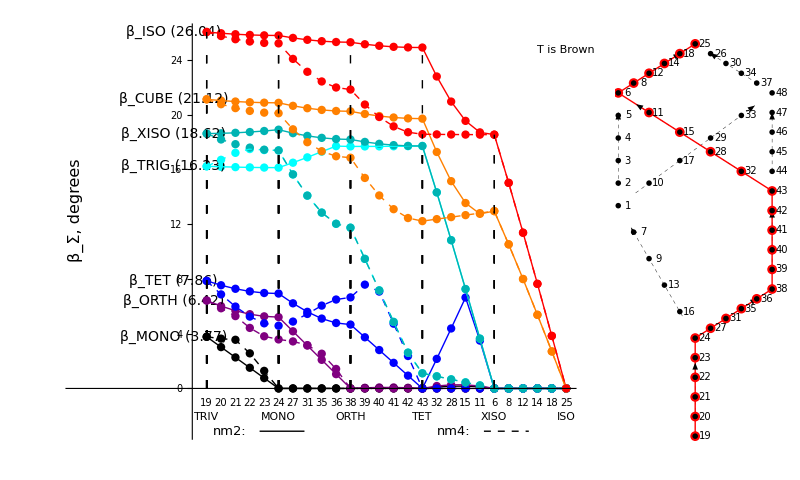

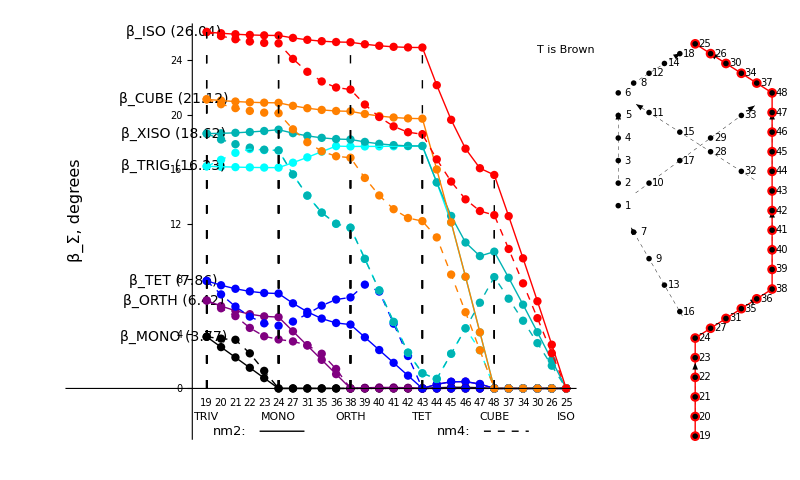

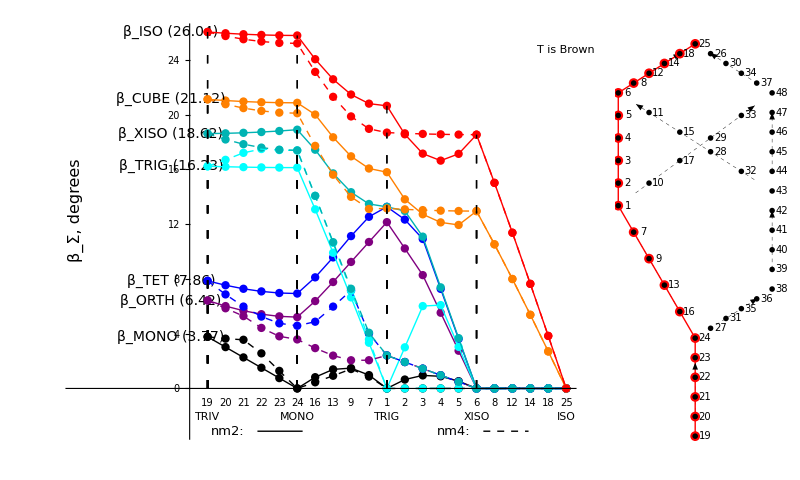

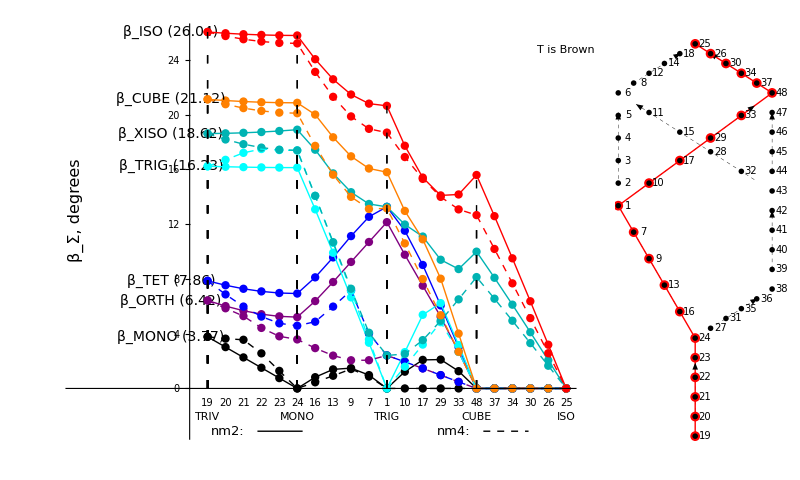

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnTETXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTETXISO]},ImageSize->800,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTETCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTETCUBE]},ImageSize->800,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIGXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIGXISO]},ImageSize->800,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIGCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIGCUBE]},ImageSize->800,Spacings->0]
```

#### Compare beta curves nm2/nm3 and nm2/nm4 (These plots do not have the whistles and bells of the plots above.)

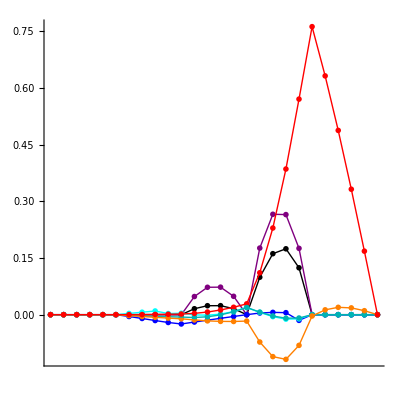

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

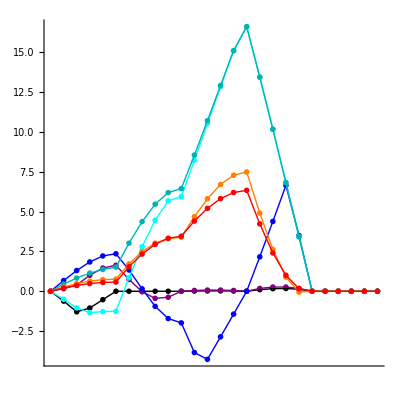

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## Igel ΣnTETXISO

Tmat is TmatIgel

Path nodes are {TRIV,MONO,ORTH,TET,XISO,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

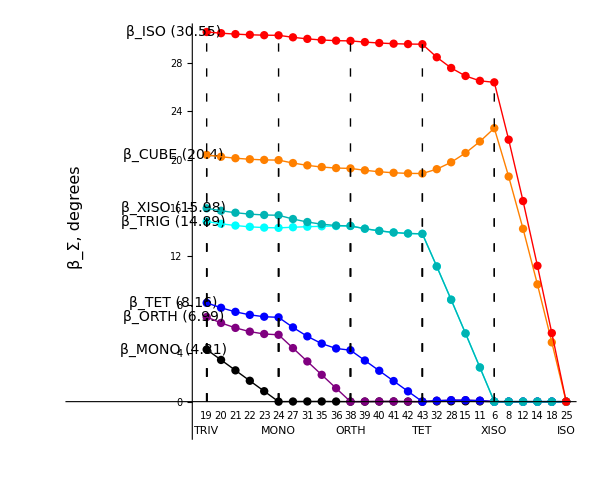

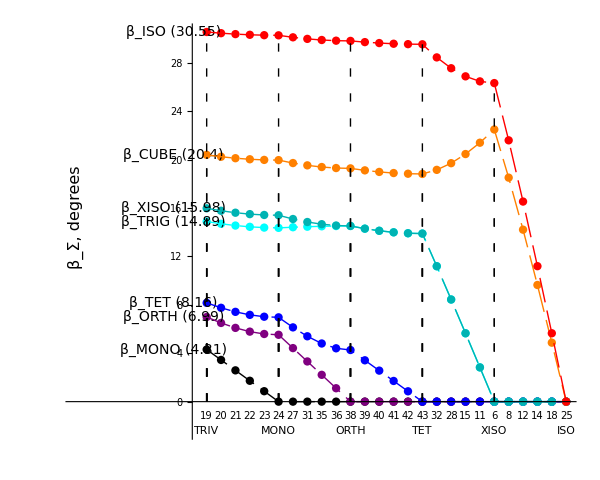

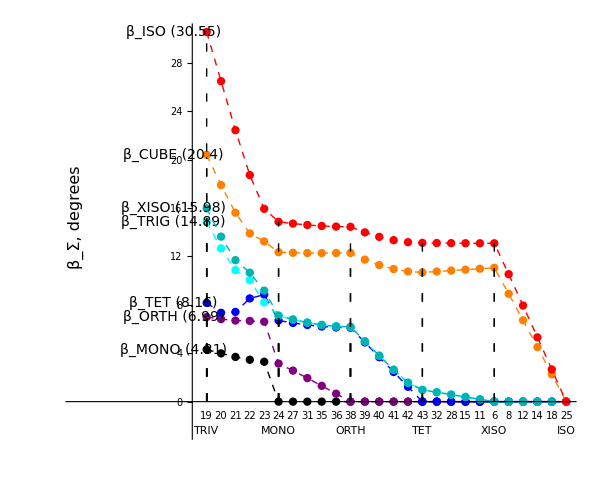

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

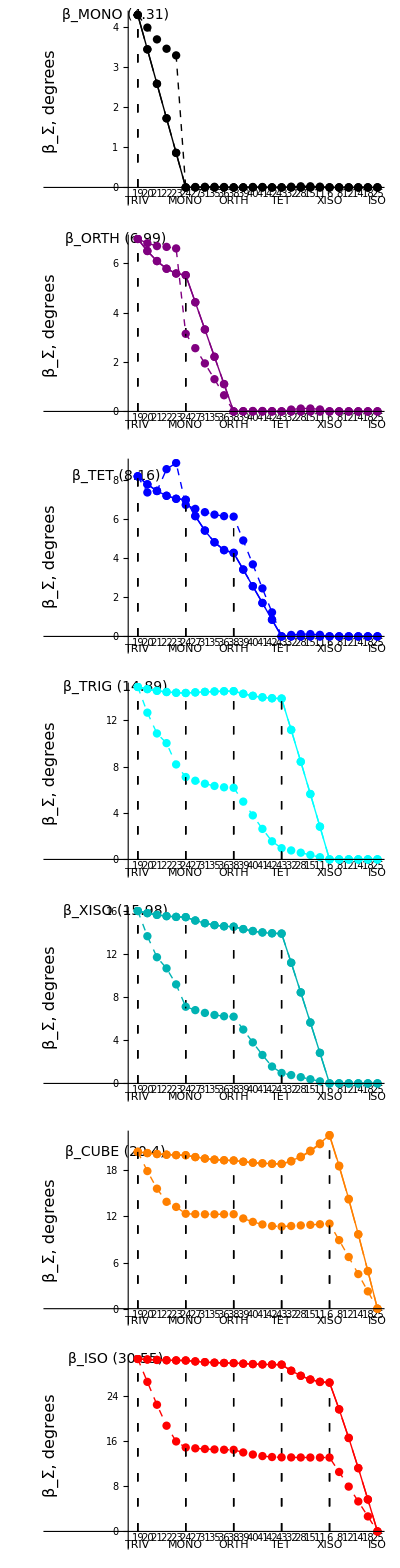

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

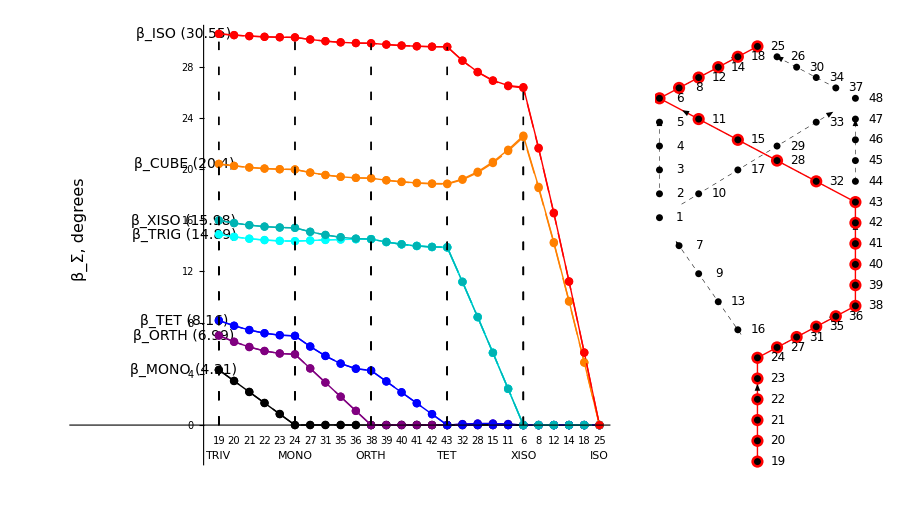

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
```

#### Three node sequences for nm2 and nm4 (based on AllPoints)

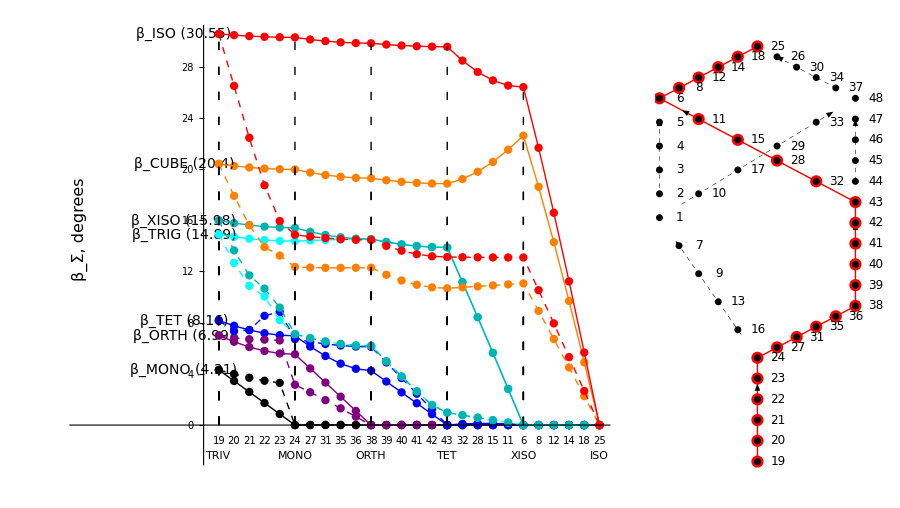

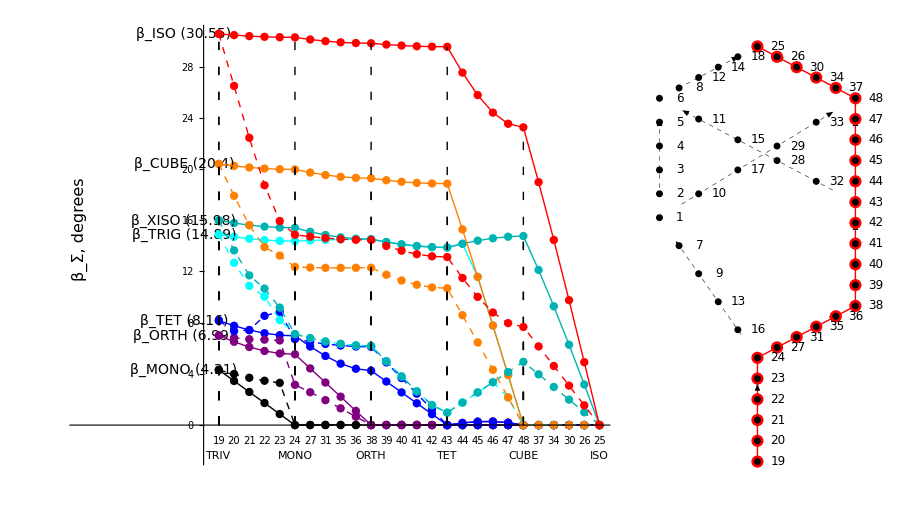

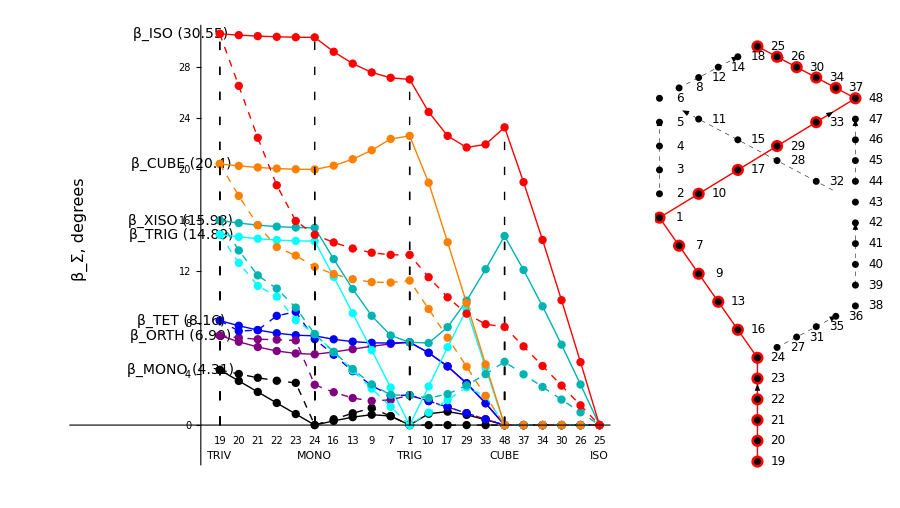

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnCUBE]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIG,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIG]},ImageSize->900,Spacings->0]
```

#### Compare beta curves for nm2 and nm3 (These plots do not have the whistles and bells of the plots above.)

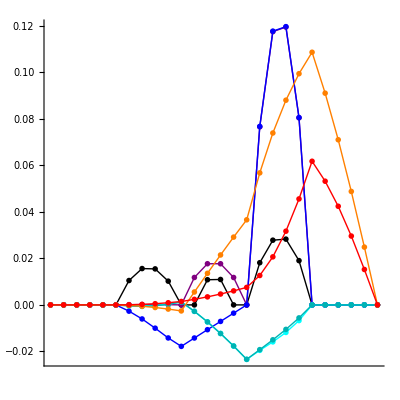

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

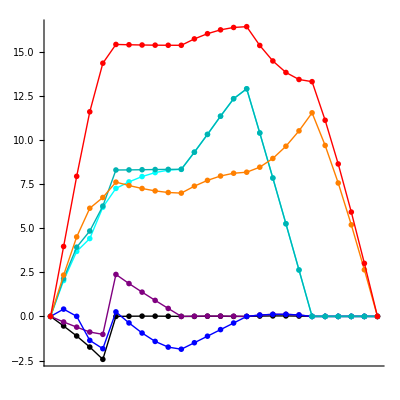

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## SSA2023 ΣnTETXISO

Tmat is TmatSSA2023

Path nodes are {TRIV,MONO,ORTH,TET,XISO,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

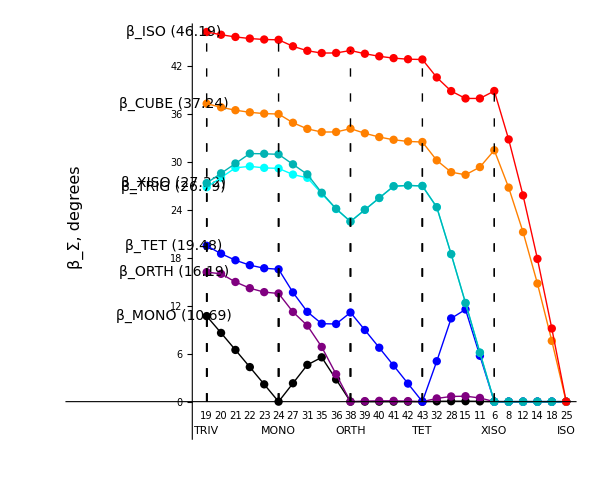

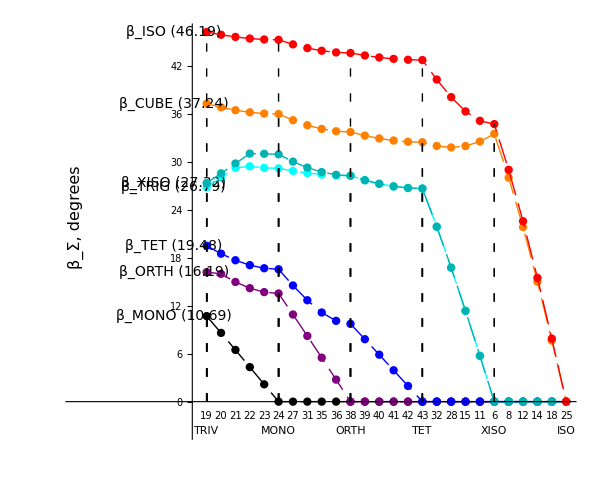

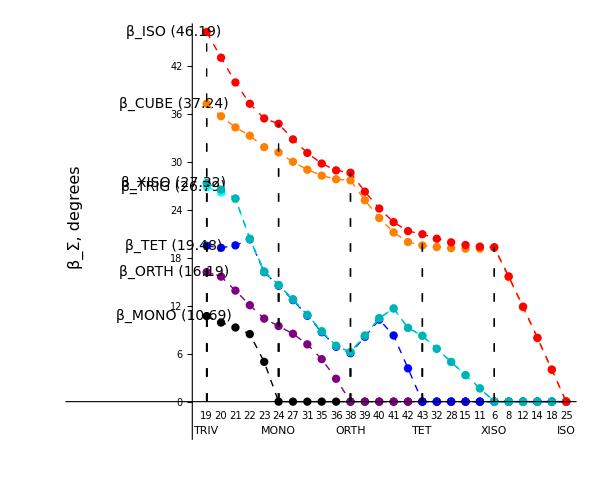

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

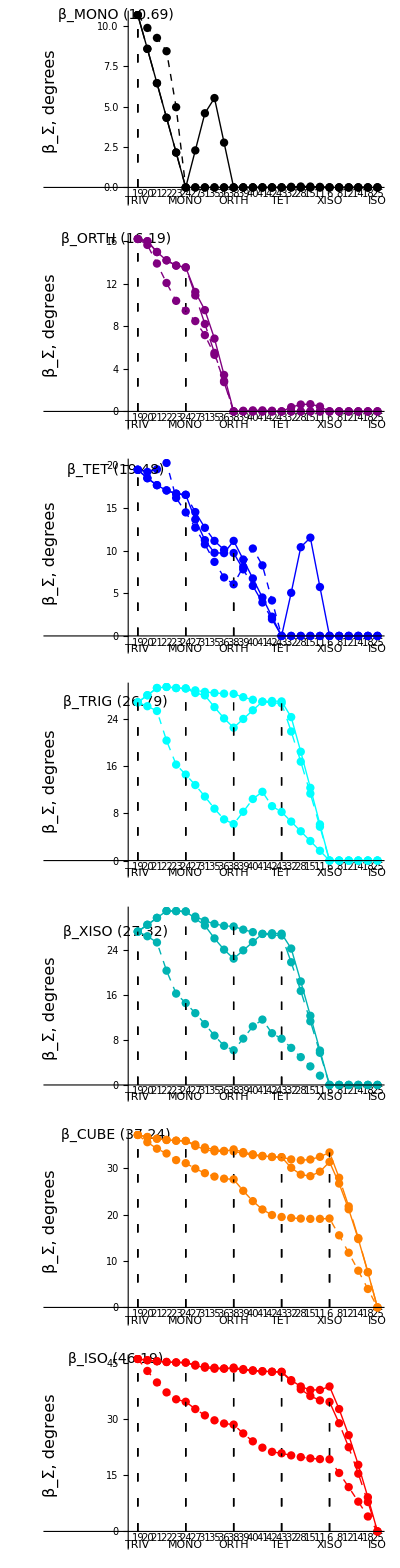

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

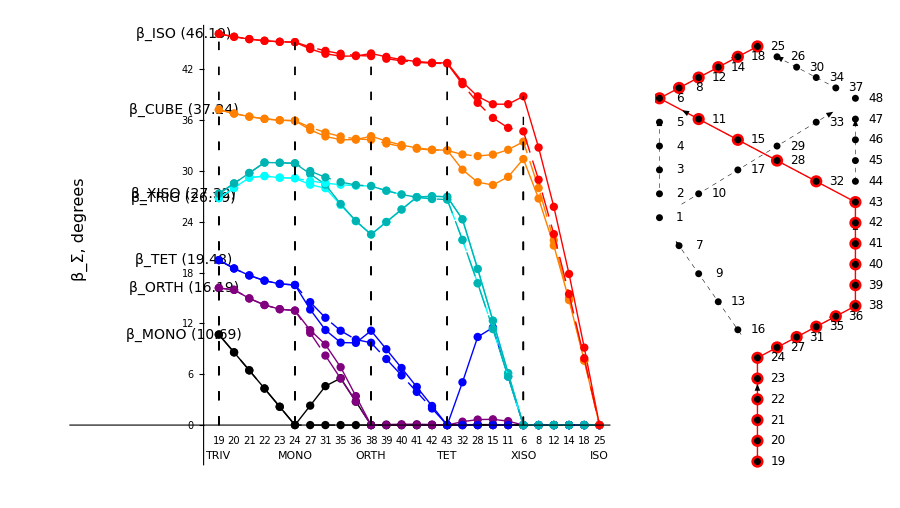

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
```

#### Three node sequences for nm2 and nm4 (based on AllPoints)

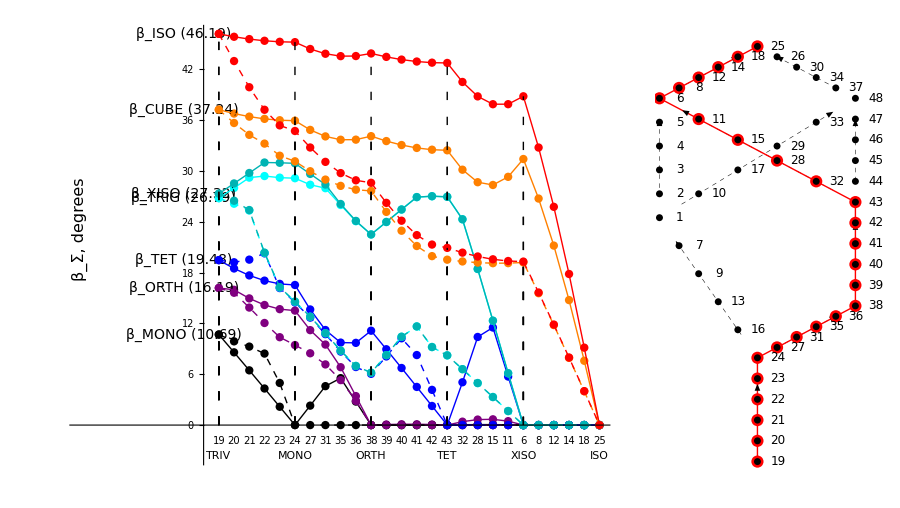

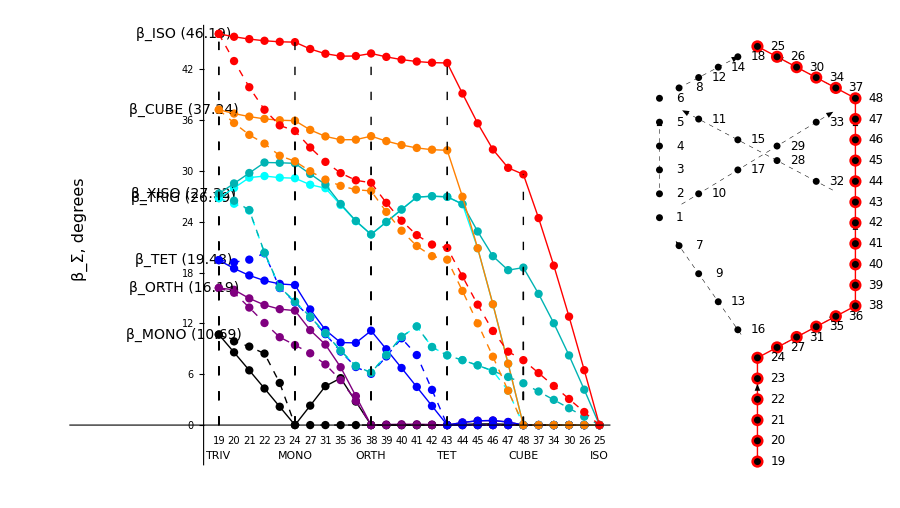

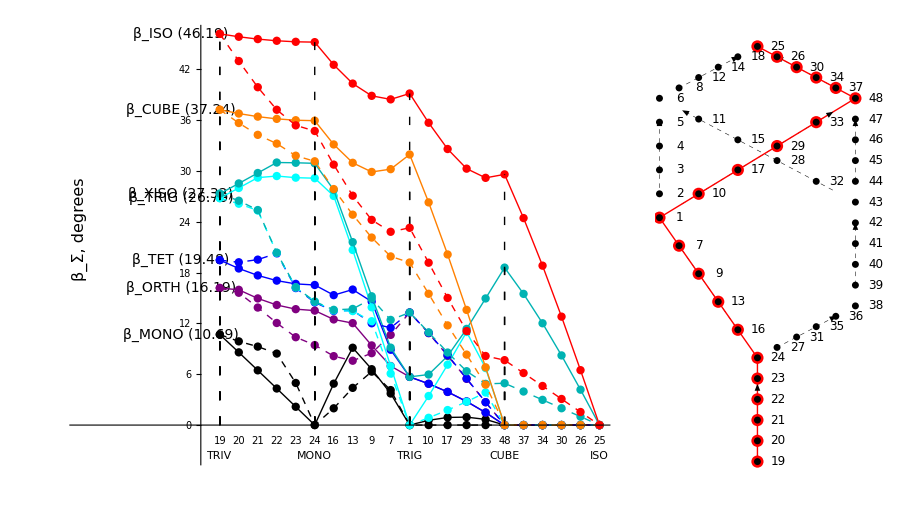

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnCUBE]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIG,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIG]},ImageSize->900,Spacings->0]
```

#### Compare beta curves for nm2 and nm3 (These plots do not have the whistles and bells of the plots above.)

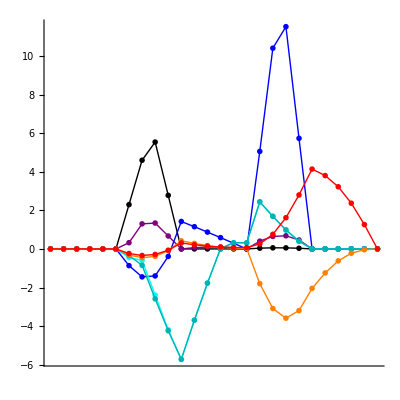

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

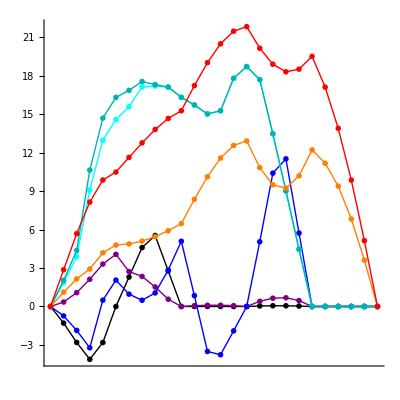

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## Mar17 ΣnTETXISO

Tmat is TmatMar17

Path nodes are {TRIV,MONO,ORTH,TET,XISO,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

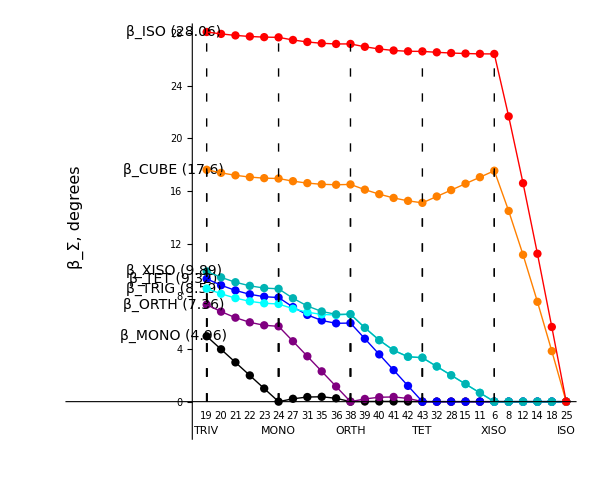

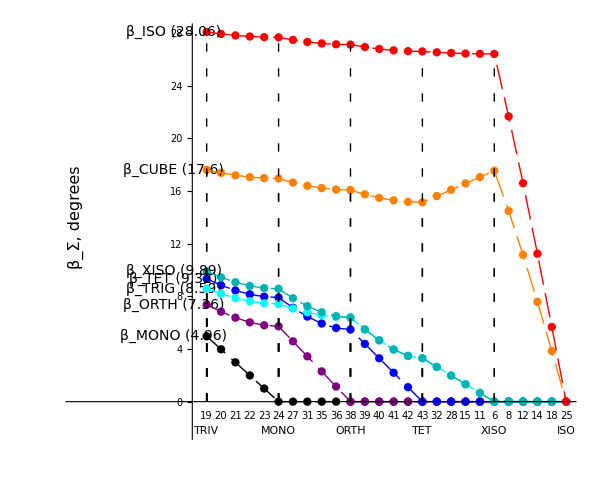

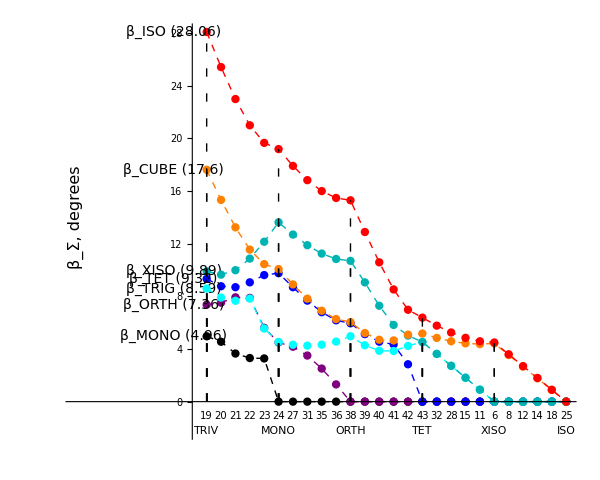

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

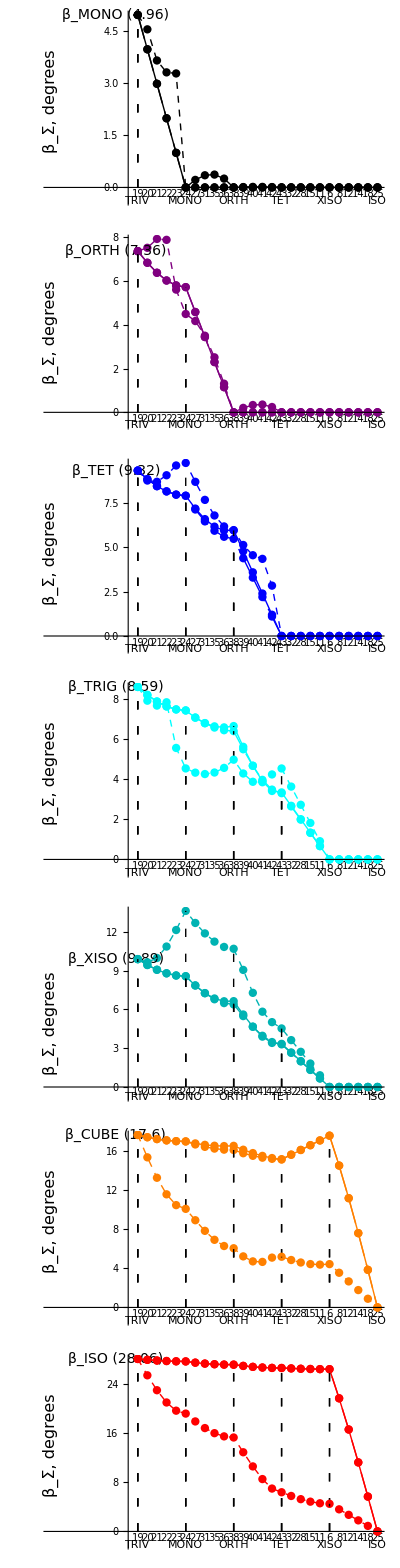

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

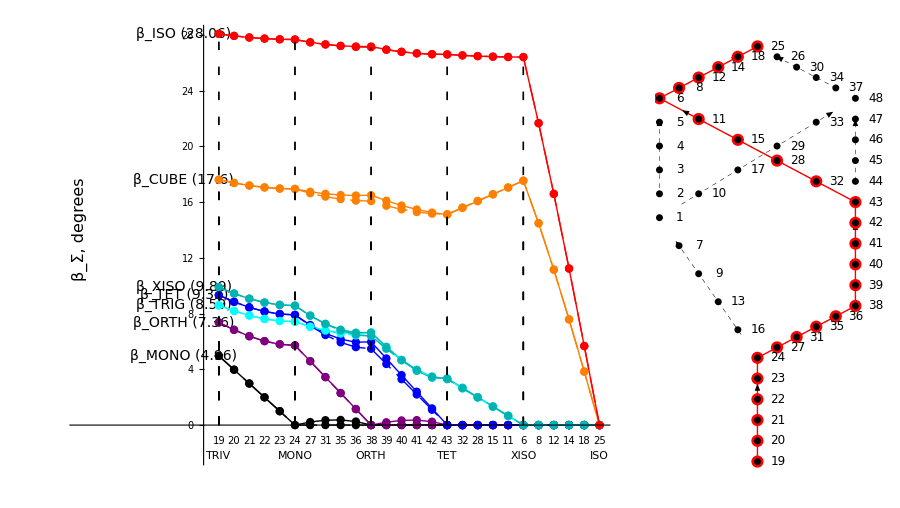

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
```

#### Three node sequences for nm2 and nm4 (based on AllPoints)

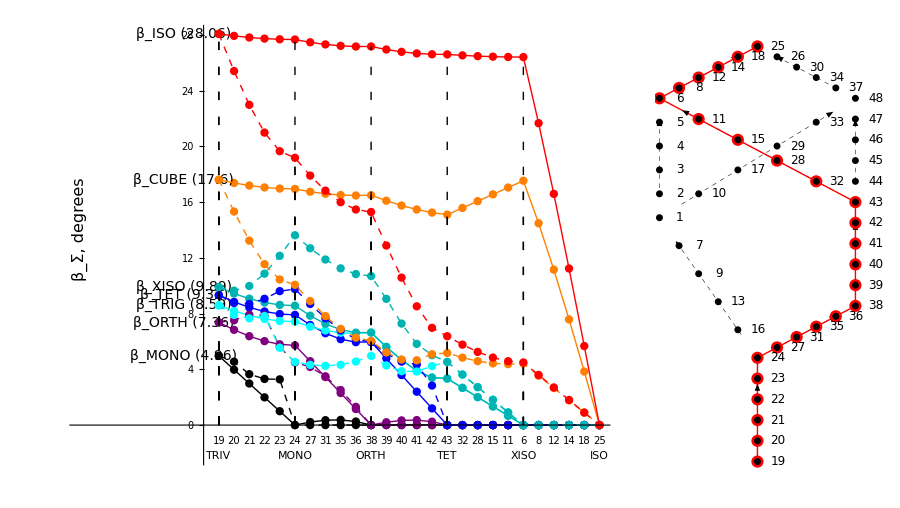

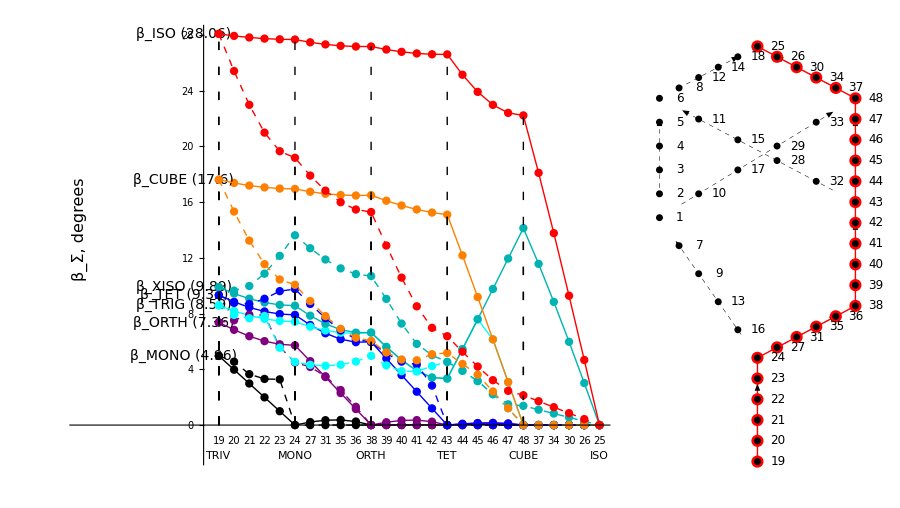

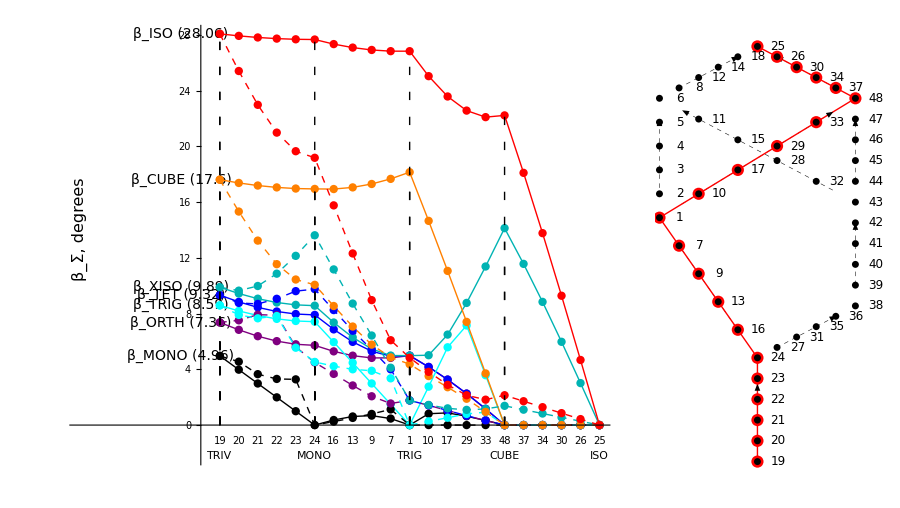

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnXISO]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnCUBE]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIG,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIG]},ImageSize->900,Spacings->0]
```

#### Compare beta curves for nm2 and nm3 (These plots do not have the whistles and bells of the plots above.)

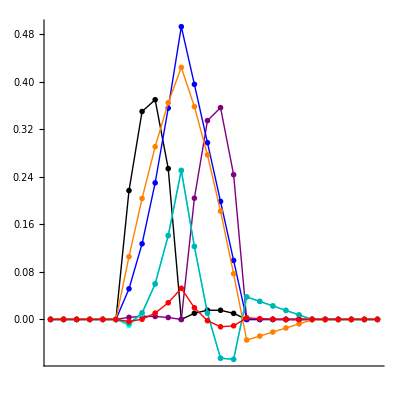

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

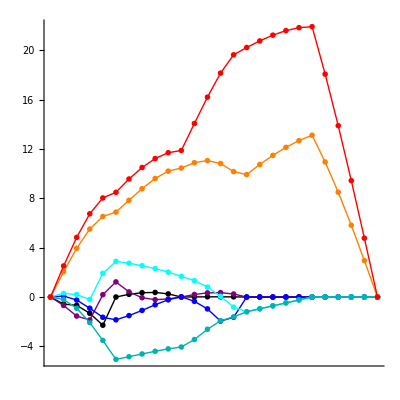

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## Node sequence ΣnTRIGCUBE

## Brown ΣnTRIGCUBE

Tmat is TmatBrownNew

Path nodes are {TRIV,MONO,TRIG,CUBE,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

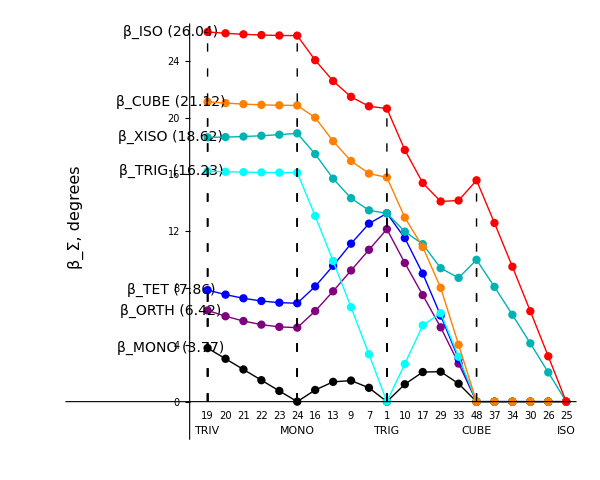

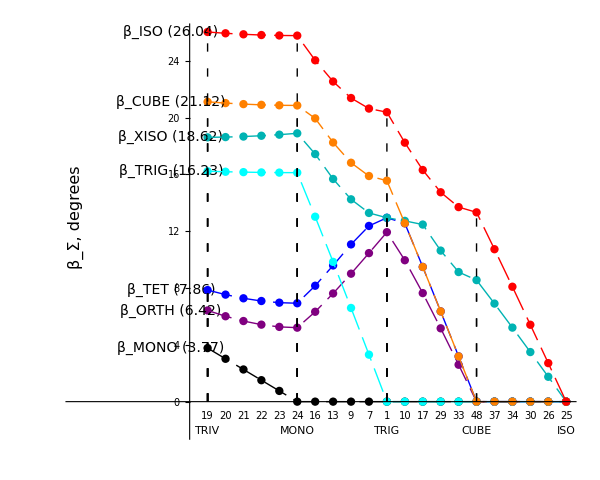

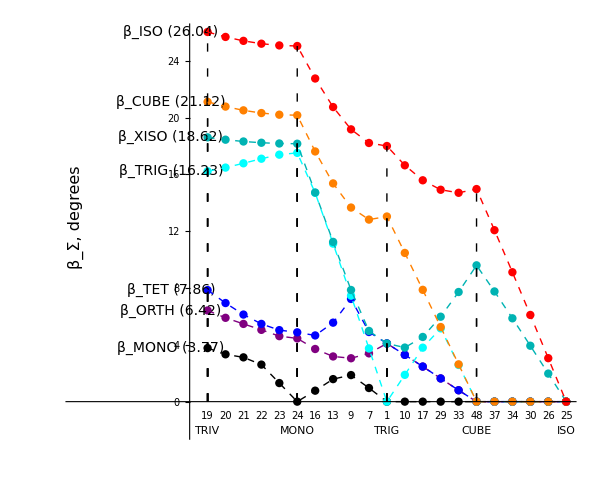

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

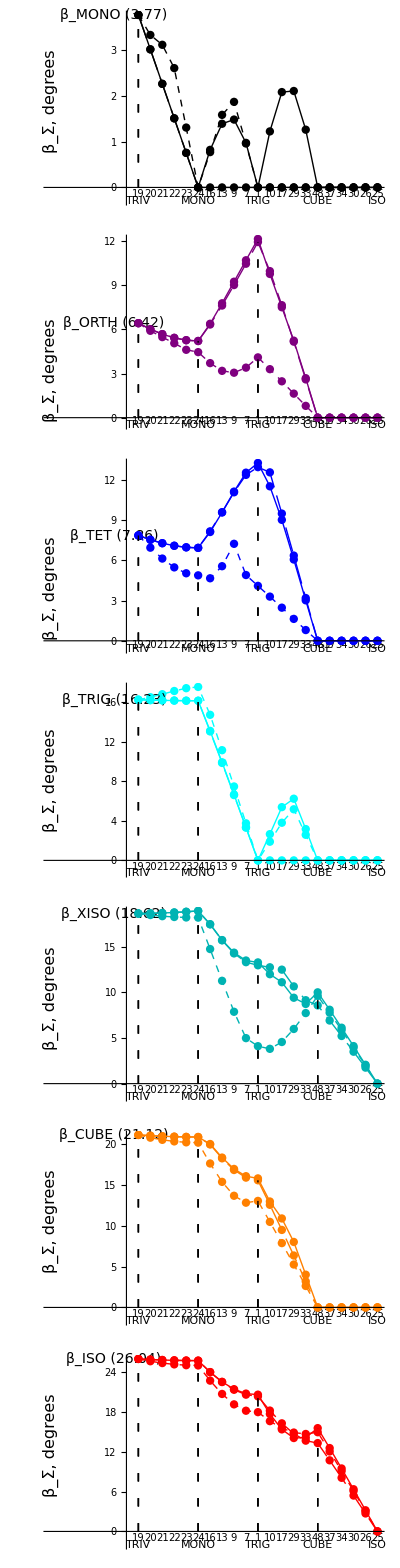

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

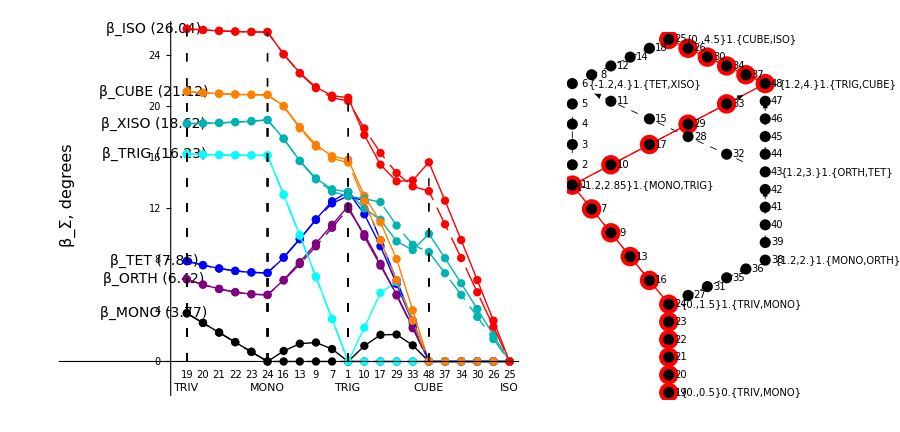

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Compare beta curves nm2/nm3 and nm2/nm4 (These plots do not have the whistles and bells of the plots above.)

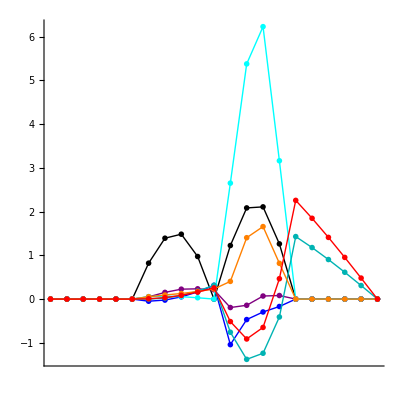

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

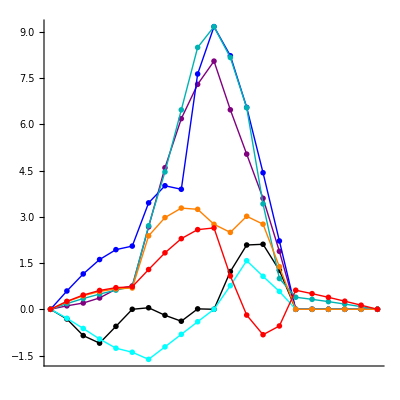

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## Igel ΣnTRIGCUBE

Tmat is TmatIgel

Path nodes are {TRIV,MONO,TRIG,CUBE,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

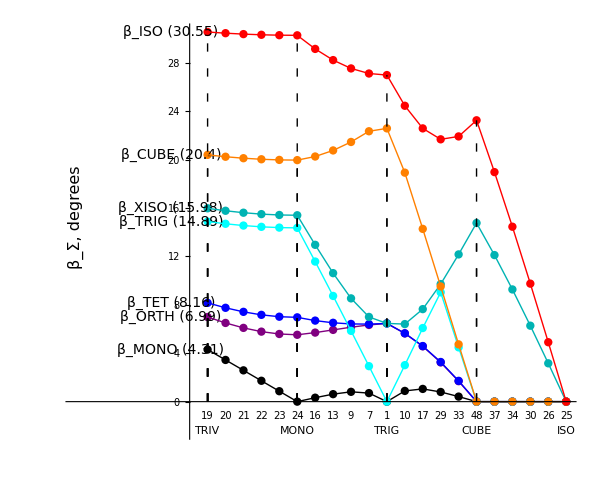

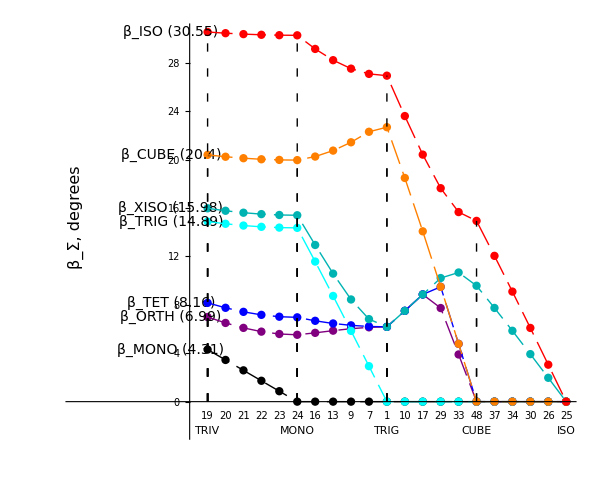

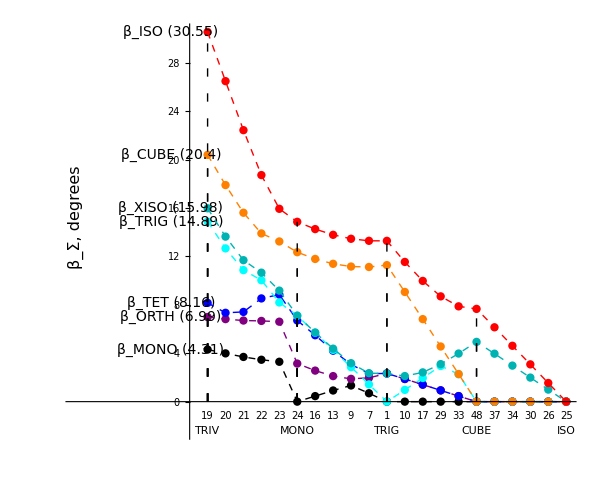

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

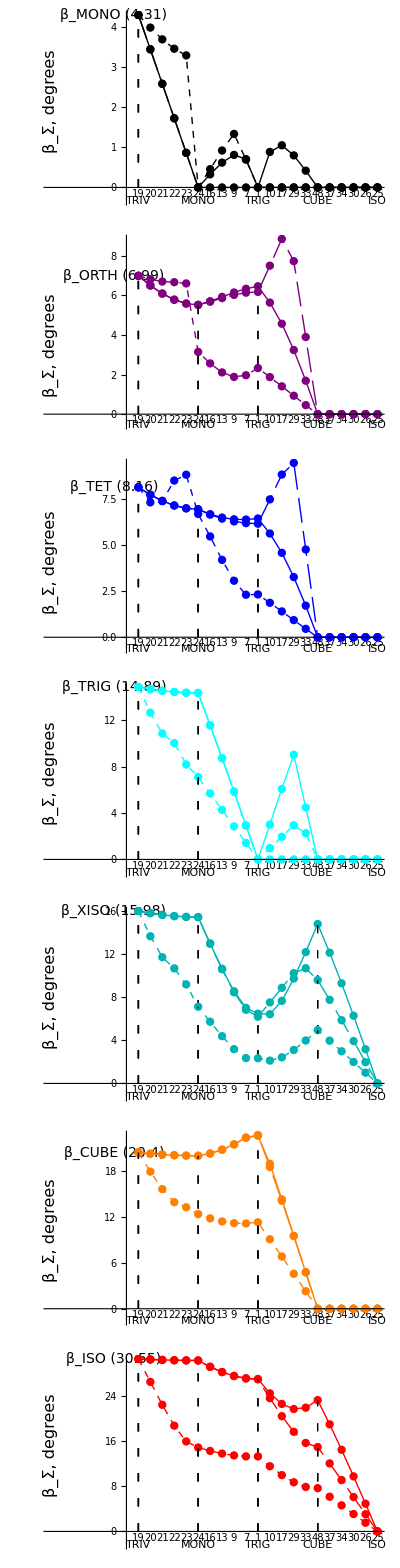

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

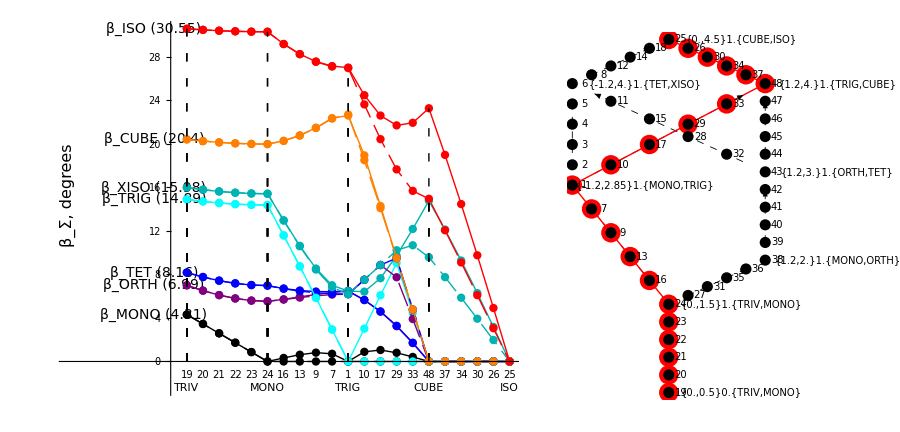

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Compare beta curves nm2/nm3 and nm2/nm4 (These plots do not have the whistles and bells of the plots above.)

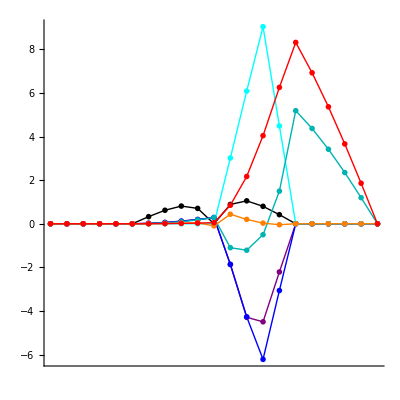

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

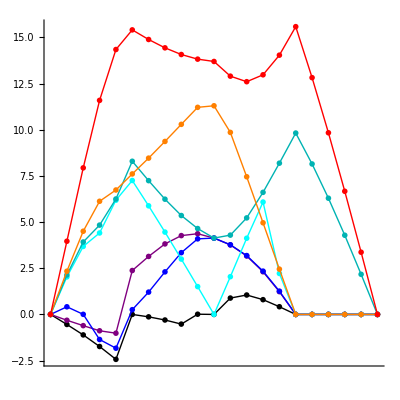

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## SSA2023 ΣnTRIGCUBE

Tmat is TmatSSA2023

Path nodes are {TRIV,MONO,TRIG,CUBE,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

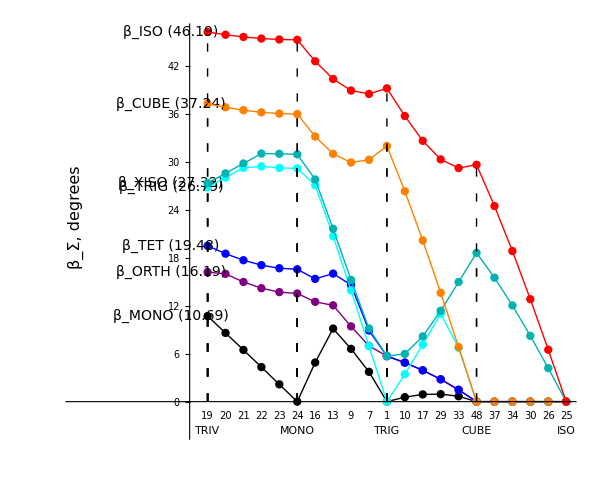

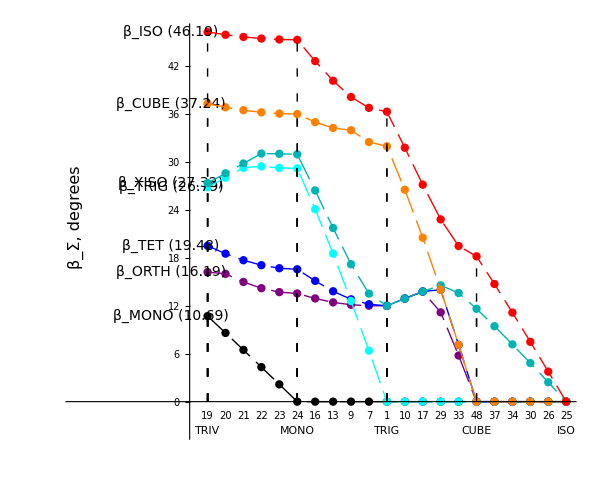

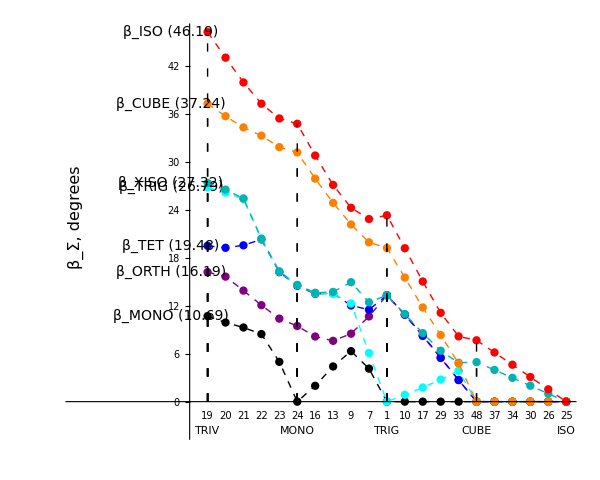

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

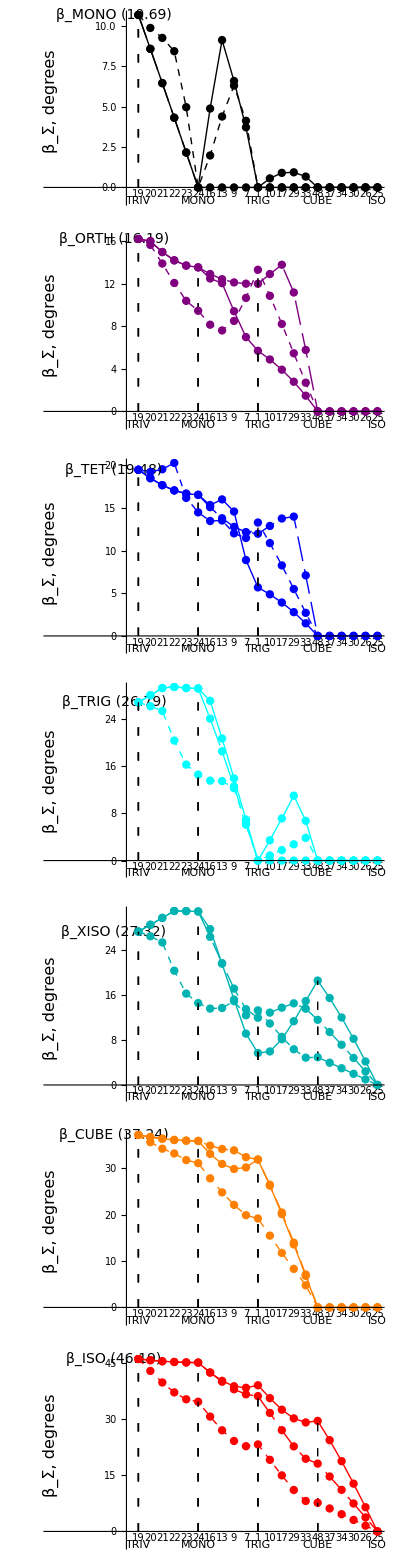

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

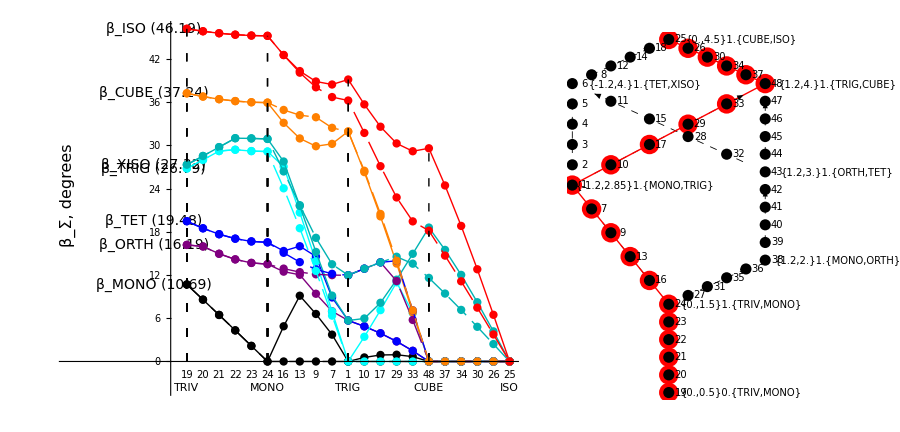

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Compare beta curves nm2/nm3 and nm2/nm4 (These plots do not have the whistles and bells of the plots above.)

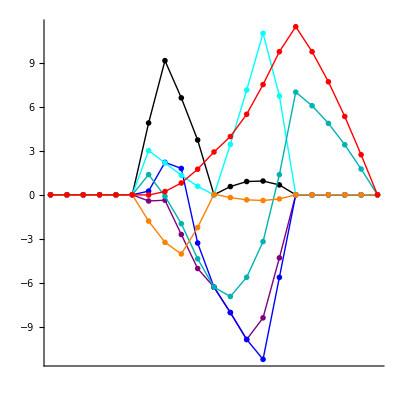

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

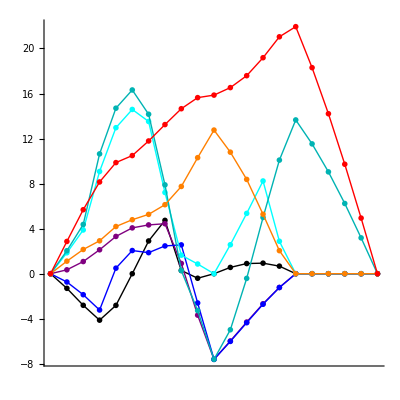

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## Mar17 ΣnTRIGCUBE

Tmat is TmatMar17

Path nodes are {TRIV,MONO,TRIG,CUBE,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

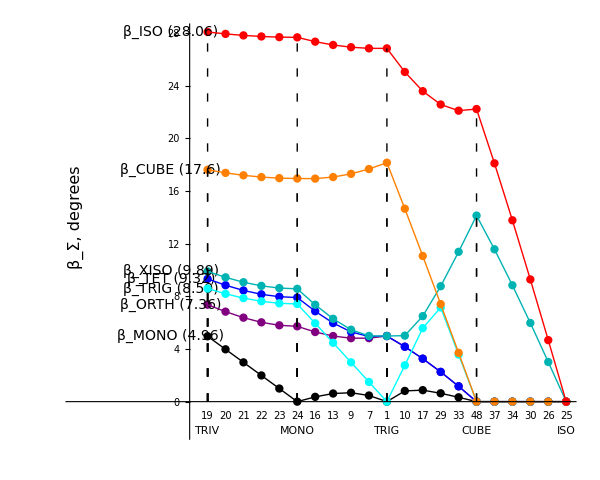

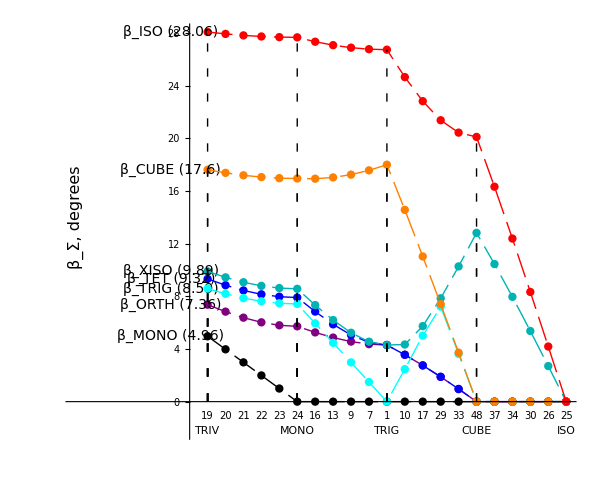

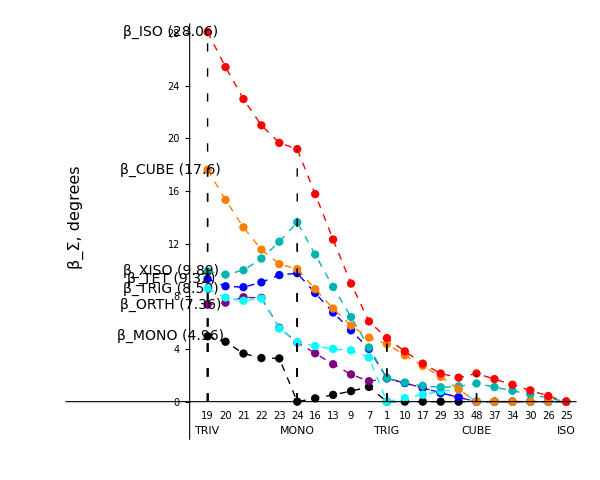

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

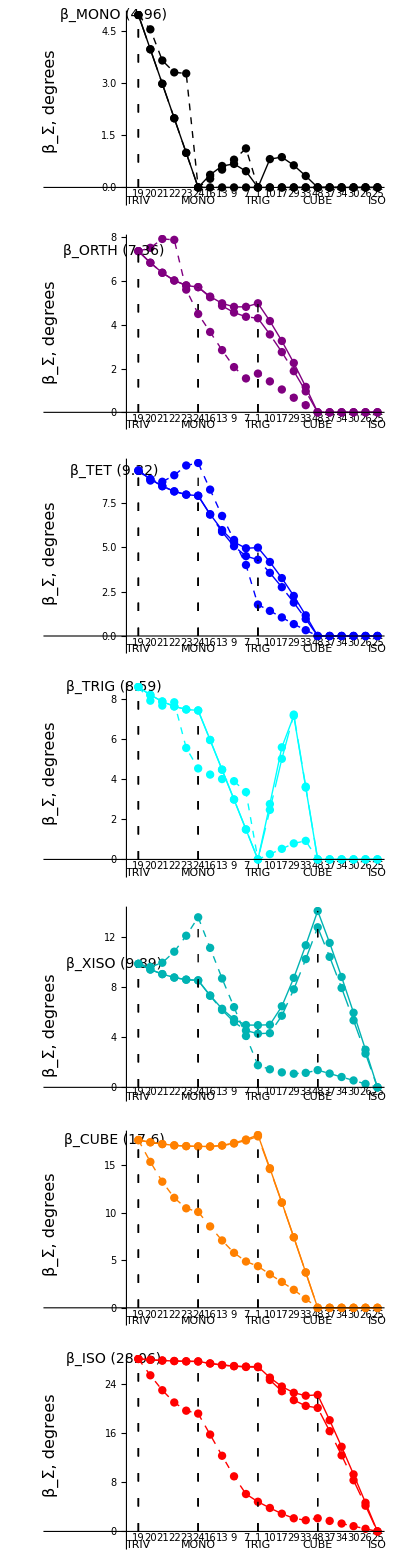

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

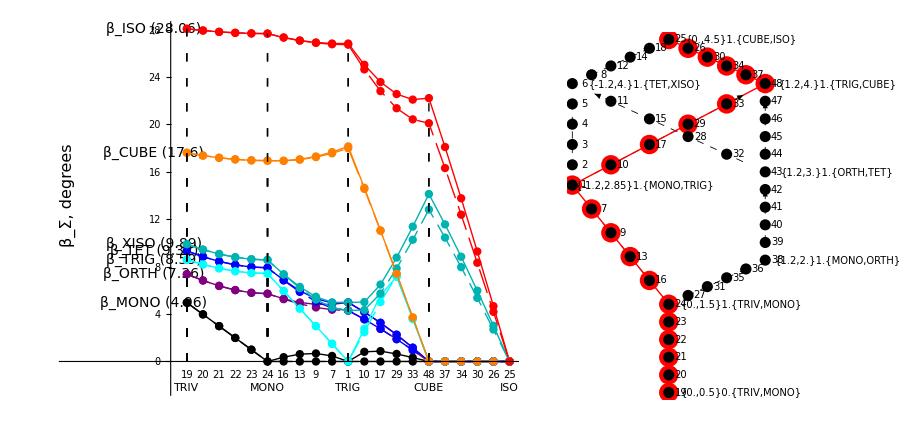

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Compare beta curves nm2/nm3 and nm2/nm4 (These plots do not have the whistles and bells of the plots above.)

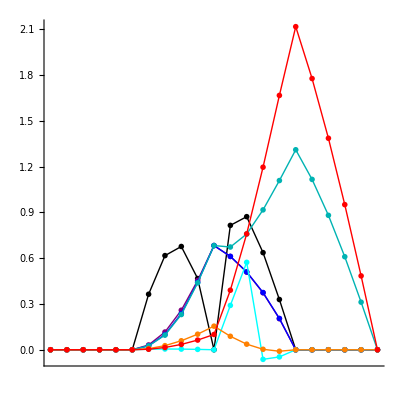

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

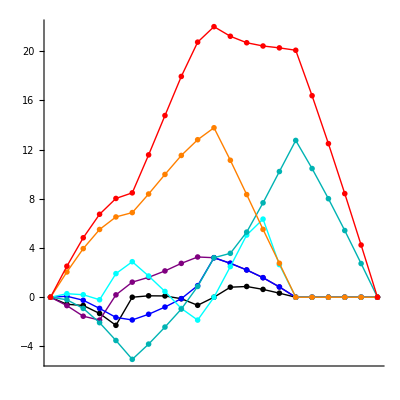

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```

## Node sequence ΣnTRIGXISO

## Brown ΣnTRIGXISO

Tmat is TmatBrown

Path nodes are {TRIV,MONO,TRIG,XISO,ISO}

dt = 0.2

UforNM4 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### separate plots for nm2, nm3, nm4 for all Σ

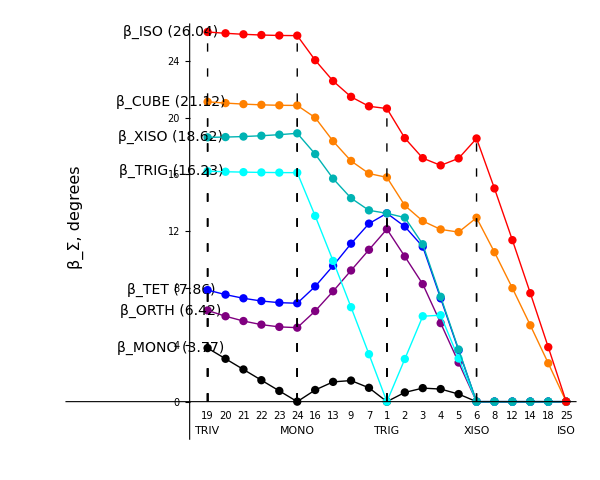

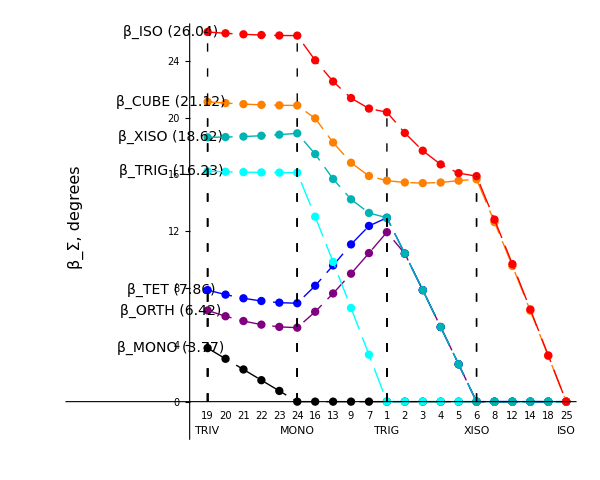

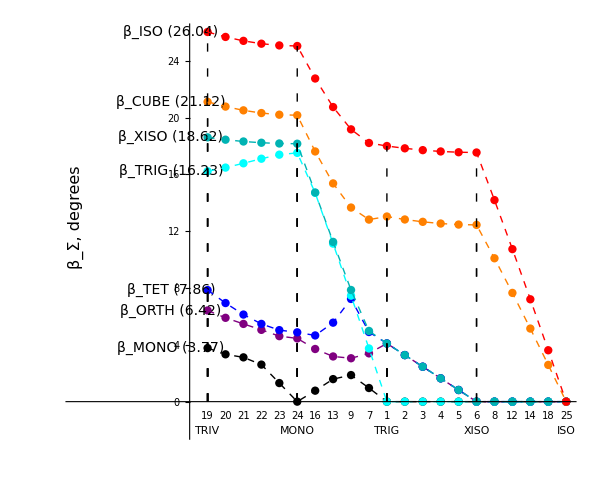

```mathematica
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","noWantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","WantNM3","noWantNM4"]
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"noWantNM2","noWantNM3","WantNM4"]
```

#### nm2, nm3, nm4 — one plot per Σ

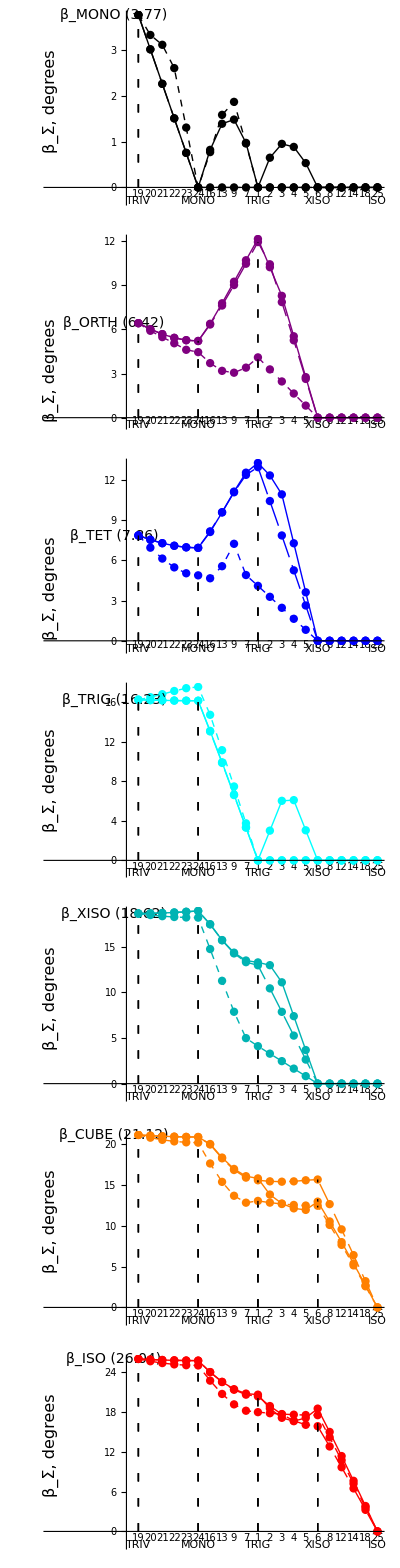

```mathematica
Column[BetaCurvesDiagram[Σn,Tmat,dt,{#},"WantNM2","WantNM3","WantNM4"]&/@ListΣ ]
```

#### nm2 and nm3 (these may be very similar)

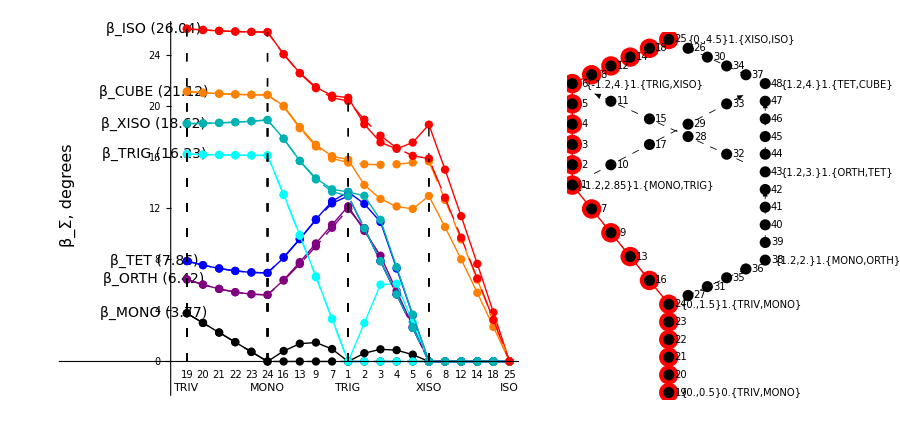

```mathematica
GraphicsRow[{
BetaCurvesDiagram[Σn,Tmat,dt,ListΣ,"WantNM2","WantNM3","noWantNM4"],
LatticeWithPts[dt,Σn]},ImageSize->900,Spacings->0]
```

#### Four node sequences for nm2 and nm4 (based on AllPoints)

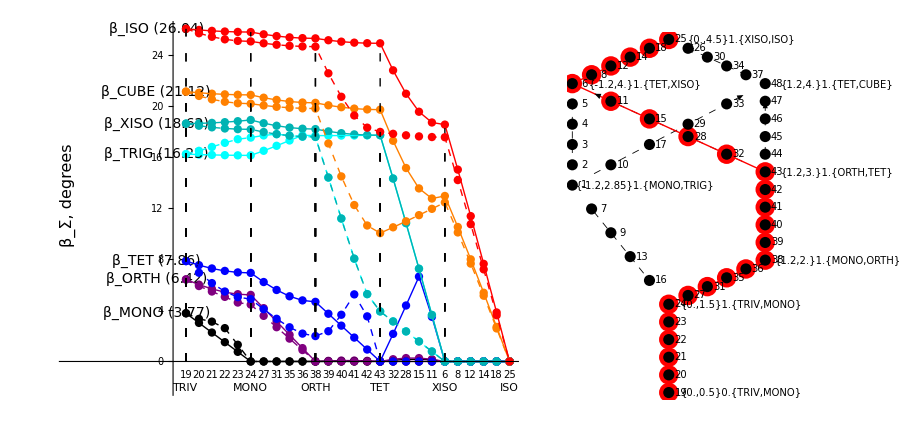

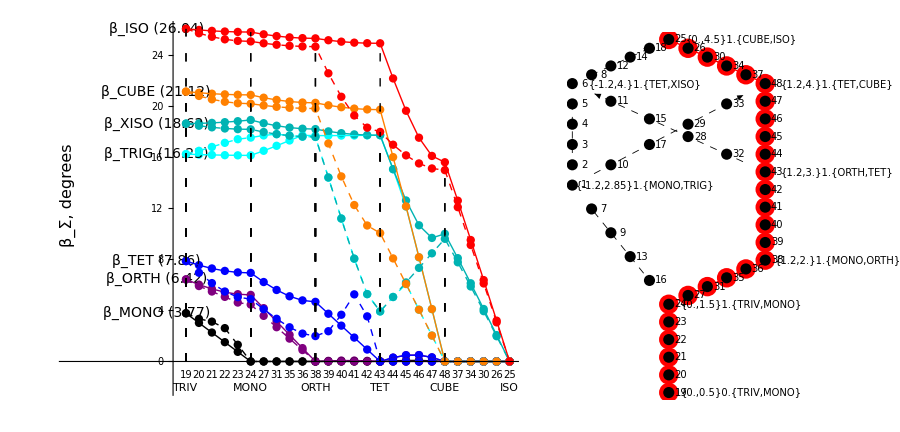

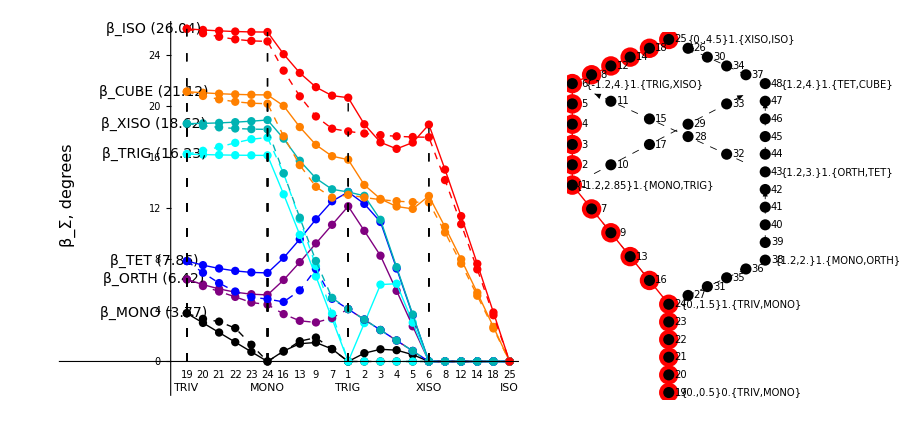

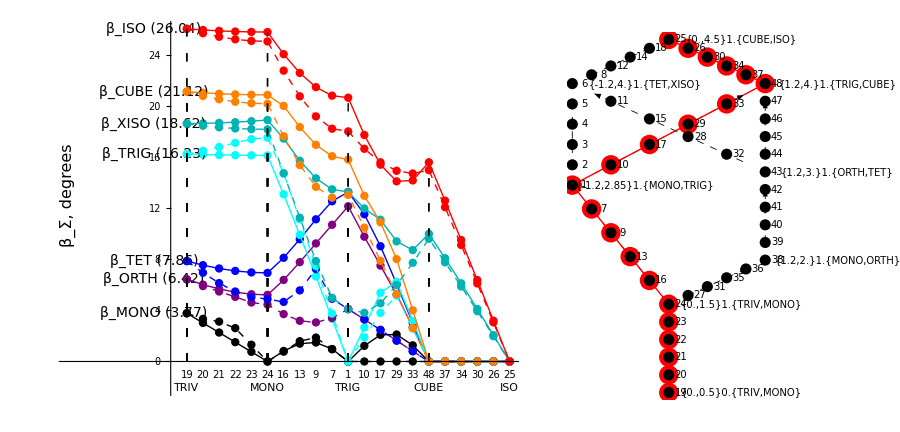

```mathematica
GraphicsRow[{
BetaCurvesDiagram[ΣnTETXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTETXISO]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTETCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTETCUBE]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIGXISO,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIGXISO]},ImageSize->900,Spacings->0]
GraphicsRow[{
BetaCurvesDiagram[ΣnTRIGCUBE,Tmat,dt,ListΣ,"WantNM2","noWantNM3","WantNM4"],
LatticeWithPts[dt,ΣnTRIGCUBE]},ImageSize->900,Spacings->0]
```

#### Compare beta curves nm2/nm3 and nm2/nm4 (These plots do not have the whistles and bells of the plots above.)

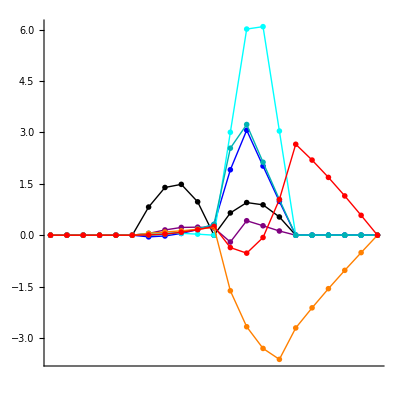

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm3,ListΣ]
```

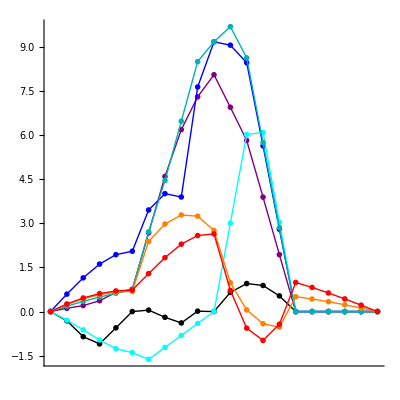

```mathematica
BetaCurvesDiffDiagram[Σn,Tmat,dt,nm2,nm4,ListΣ]
```